```mathematica
k1:=0.1
S:=1
Kd:=1
kdr:=0.1
m:=2
ksy:=1
k2:=0.1
ET:=1
Km:=1
```

```mathematica
eqn1 = {r'[t]==k1*S*Kd^m/(Kd^m+p[t-24]^m)-kdr*r[t]}
eqn2 ={p'[t]==ksy*r[t]-k2*ET*p[t]/(Km+p[t])}
eqn3 ={p'[t]==ksy*r[t]-k2*ET*p[t]}
initCond ={r[0]==0, p[0]==0}
diffeqns= Join[eqn1,eqn3]
```

{r'[t]==0.1/(1+p[-24+t]^2)-0.1 r[t]}

{p'[t]==-(0.1 p[t])/(1+p[t])+r[t]}

{p'[t]==-0.1 p[t]+r[t]}

{r[0]==0,p[0]==0}

{r'[t]==0.1/(1+p[-24+t]^2)-0.1 r[t],p'[t]==-0.1 p[t]+r[t]}

```mathematica
Solution = NDSolve[Join[diffeqns, initCond],{r,p},{t,0,3000}]
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t ≤ 0..

{{r→InterpolatingFunction[{{0., 3000.}}, <>],p→InterpolatingFunction[{{0., 3000.}}, <>]}}

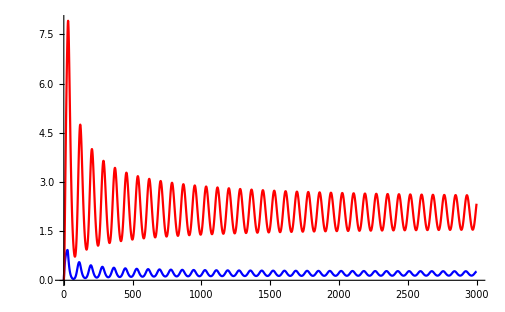

```mathematica
Plot[{{r[t]}/.Solution, {p[t]}/.Solution},{t,0,3000},PlotRange->All,PlotStyle->{Blue,Red}]
```

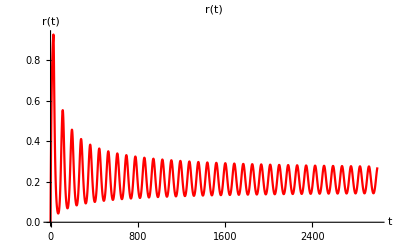

```mathematica
Plot[{r[t]}/.Solution,{t,0,3000},PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->r[t],AxesLabel->{t,r[t]}]
```